## Old

```mathematica
Clear[d,n,i];
d=Table[{i, 100 - (100*(1-i/10))},{i,1,10}]
```

{{1,10},{2,20},{3,30},{4,40},{5,50},{6,60},{7,70},{8,80},{9,90},{10,100}}

```mathematica
n=Length[d]
```

10

```mathematica
Clear[df,i];
df[i_]:=d[[i+1,2]];
```

```mathematica
kappa = Log[101]/Log[n]
```

Log[101]/Log[10]

```mathematica
Table[(101-i^kappa),{i,1,n}] // N
```

{100.,96.988,91.9572,84.9039,75.8255,64.7202,51.5862,36.4223,19.2272,0.}

```mathematica
Table[46 ( Exp[i]-1 )/( Exp[n] - 1),{i,0,n}] // N
```

{0.,0.00358862,0.0133435,0.03986,0.111939,0.307871,0.840469,2.28822,6.22362,16.9211,46.}

```mathematica
Clear[now,n];
now = 100;
n= 10;
Table[ {i,now-i^(Log[now]/Log[n])},{i,0,n-1}] // N
```

{{0.,100.},{1.,99.},{2.,96.},{3.,91.},{4.,84.},{5.,75.},{6.,64.},{7.,51.},{8.,36.},{9.,19.}}

```mathematica
Clear[now,n];
now = 81;
n= 10;
Table[ {i,19+now-i^(Log[now]/Log[n])},{i,0,n-1}] // N
```

{{0.,100.},{1.,99.},{2.,96.2459},{3.,91.8609},{4.,85.9064},{5.,78.4239},{6.,69.4445},{7.,58.9931},{8.,47.0905},{9.,33.7543}}

```mathematica
Clear[n,i];
Simplify[Log[n-i]/Log[n]]
```

Log[-i+n]/Log[n]

```mathematica
Clear[now,n];
now = 100;
n= 10;
Table[ {i,now/Log[n] Log[n-i]},{i,0,n-1}] // N
```

{{0.,100.},{1.,95.4243},{2.,90.309},{3.,84.5098},{4.,77.8151},{5.,69.897},{6.,60.206},{7.,47.7121},{8.,30.103},{9.,0.}}

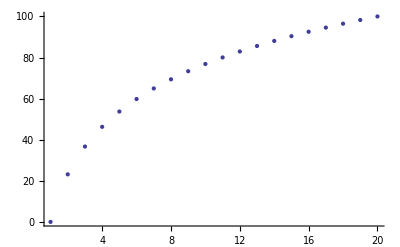

```mathematica
ListPlot[Table[Log[x]/Log[20] 100,{x,1,20}]]
```

```mathematica
Max[testdata]
```

90

## Newer

```mathematica
Clear[maxbackups,i,minpos,iterate,d,maxtime,keephead,allopts,fitfun,minpposlow,calibrate,refine,addbackup,testdata];
```

```mathematica
maxbackups=10;
maxtime=355;
keephead = 3;
```

```mathematica
allopts[d_]:=If[Length[d]≤maxbackups,{d},
Table[Drop[d,{i}],{i,1,Length[d]}]];
```

```mathematica
fitfun[d_]:=Sum[Abs[d⟦i+1⟧ - (maxtime/Log[Length[d]] * Log[Length[d]-i])],{i,0,Length[d]-1}]
```

```mathematica
minpposlow[f_]:=Flatten[Position[f,Min[f]]]⟦1⟧;
minpos[f_]:=keephead + minpposlow[Table[f[[i]],{i,keephead+1,Length[f]}]];
calibrate[alld_]:=Table[alld[[i]]-Min[alld[[i]]],{i,1,Length[alld]}];
refine[d_]:=allopts[d]⟦ minpos[Map[fitfun,calibrate[allopts[d]]]]⟧;
addbackup[d_]:=Sort[Join[{Random[Integer,{Max[d],Max[d]+5}]},d],Greater];
iterate[d_,0]:=refine[addbackup[d]];
iterate[d_,n_]:=refine[addbackup[iterate[d,n-1]]];
```

```mathematica
testdata=Sort[{1,2,4,10,13,18,30,35,39,50,90},Greater];
refine[testdata]
```

{90,50,39,35,30,18,13,10,4,1}

```mathematica
iterate[%,20]
```

{149,145,140,140,140,135,130,126,107,1}

```mathematica
iterate[%,50]
```

{295,290,290,287,277,249,214,171,107,1}

```mathematica
iterate[%,100]
```

{553,550,546,301,277,249,214,171,107,1}

## Newest

```mathematica
Clear[maxbackups,i,minpos,iterate,d,maxtime,keephead,allopts,fitfun,minpposlow,calibrate,refine,addbackup,testdata];
```

```mathematica
Clear[n,maxtime];
n=10;
maxtime=355;
Table[ Log[i+1]/Log[n] maxtime,{i,0,n-1}] // N
```

{0.,106.866,169.378,213.731,248.134,276.244,300.01,320.597,338.756,355.}

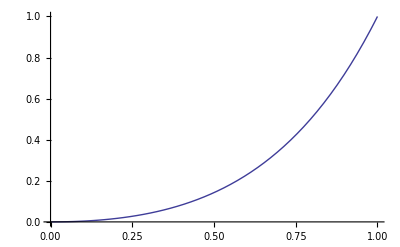

```mathematica
Plot[((Exp[x]-Exp[0])/(Exp[1]-Exp[0]))^2,{x,0,1}]
```

```mathematica
maxtime = 100;
maxbackups = 10;
keephead = 2;
```

```mathematica
allopts[d_]:=If[Length[d]≤maxbackups,{d},
Table[Drop[d,{i}],{i,1,Length[d]}]];
```

```mathematica
fitfun[d_]:=Sum[(d⟦i+1⟧ - (maxtime *((Exp[i/(Length[d]-1)] -1 )/(Exp[1]-1))^2))^2,{i,0,Length[d]-1}]
```

```mathematica
minpposlow[f_]:=Flatten[Position[f,Min[f]]]⟦1⟧;
minpos[f_]:=keephead + minpposlow[Table[f[[i]],{i,keephead+1,Length[f]}]];
calibrate[alld_]:=Table[alld[[i]]-Min[alld[[i]]],{i,1,Length[alld]}];

refine[d_]:=If[Max[d]>maxtime,
Drop[d,{Length[d]}],
allopts[d]⟦ minpos[Map[fitfun,calibrate[allopts[d]]]]⟧];

addbackup[d_]:=calibrate[{Sort[Join[{Random[Integer,{-4,0}]},d]]}][[1]];
iterate[d_,0]:=refine[addbackup[d]];
iterate[d_,n_]:=refine[addbackup[iterate[d,n-1]]];
```

```mathematica
testdata=Sort[{0,1,2,4,10,18,30,35,39,50,90}];
refine[testdata]
```

{0,1,2,4,10,18,30,39,50,90}

```mathematica
iterate[%,0]
```

{0,1,2,5,11,19,31,40,51,91}

```mathematica
iterate[%,50]
```

{0,4,8,9,10,14,23,41,67,87}

## for unit tests

```mathematica
testdata=Sort[{0,1,2,4,10,18,30,35,39,50,90}]
```

{0,1,2,4,10,18,30,35,39,50,90}

```mathematica
Clear[td2];
td2 = calibrate[{Join[{-1},testdata]}][[1]]
```

{0,1,2,3,5,11,19,31,36,40,51,91}

```mathematica
td3 = Drop[td2,1]
```

{1,2,3,5,11,19,31,36,40,51,91}

```mathematica
Clear[vals];vals = Table[(td3[[i+1]] - (maxtime *((Exp[i/(Length[td3]-1)] -1 )/(Exp[1]-1))^2))^2,{i,0,Length[td3]-1}] // N
```

{1.,2.64183,1.79489,0.729845,7.88042,22.5274,65.7425,1.42159,118.17,447.635,81.}

```mathematica
Sum[vals[[i]],{i,1,Length[vals]}]
```

750.543

```mathematica
fitfun[td3] // N
```

750.543

```mathematica
fitfun[{1,2,3,5,11,19,31,36,40,51,91}]//N
```

750.543

```mathematica
Map[fitfun,calibrate[allopts[td2]]] // N
```

{800.252,749.543,747.292,745.613,746.196,748.509,736.568,685.972,699.049,802.014,1388.48,3708.48}

### Test refine (aka incremented in the C++ code)

```mathematica
refine[td2]
```

{0,1,2,3,5,11,19,36,40,51,91}

### Test two iterations

```mathematica
refine[refine[td2]]
```

{0,1,2,5,11,19,36,40,51,91}

### Fitfun

```mathematica
(17 - (maxtime *((Exp[5/(maxbackups-1)] -1 )/(Exp[1]-1))^2))^2 // N
```

2.86675

### Many iterations

```mathematica
testdata2=Sort[{0,1,2,4,10,18,30,39,50,90}]
```

{0,1,2,4,10,18,30,39,50,90}

```mathematica
Clear[step];
step[d_]:=refine[calibrate[{Join[{-1},d]}][[1]]];
```

```mathematica
Nest[step,testdata2,200]
```

{0,1,2,5,8,18,34,44,54,83}

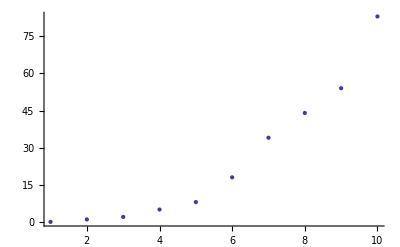

```mathematica
ListPlot[%]
```